```mathematica
SetDirectory[NotebookDirectory[]];
ClearAll["Global`*"]
```

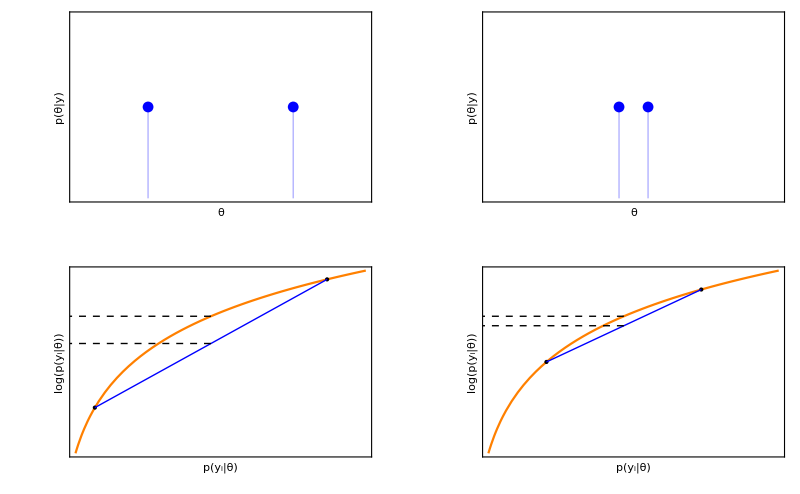

```mathematica
{x1,x2} = {1,7};
p1 = {x1,Log[x1]};
p2={x2,Log[x2]};
xbar = Mean@{x1,x2};
{x3,x4} = {2,6};
p3 = {x3,Log[x3]};
p4={x4,Log[x4]};
xbar2 = Mean@{x3,x4};
g1=Show[Plot[Log[x],{x,0.5,8},Axes->None,Frame->{True,True,False,False},PlotStyle->Orange,FrameTicks->{None,None},FrameLabel->{"p(y_i|θ)","log(p(y_i|θ))"},BaseStyle->{FontSize->14},Epilog->{{PointSize->Large,Point/@{p1,p2}},{Blue,Line@{p1,p2}},{Dashed,Line[{{xbar,Log@xbar},{0,Log@xbar}}],Line[{{xbar,0.5Total@(Log/@{x1,x2})},{0,0.5Total@(Log/@{x1,x2})}}]}}],ImageSize->800];
g2=Show[Plot[Log[x],{x,0.5,8},Axes->None,Frame->{True,True,False,False},PlotStyle->Orange,FrameTicks->{None,None},FrameLabel->{"p(y_i|θ)","log(p(y_i|θ))"},BaseStyle->{FontSize->14},Epilog->{{PointSize->Large,Point/@{p3,p4}},{Blue,Line@{p3,p4}},{Dashed,Line[{{xbar2,Log@xbar2},{0,Log@xbar2}}],Line[{{xbar2,0.5Total@(Log/@{x3,x4})},{0,0.5Total@(Log/@{x3,x4})}}]}}],ImageSize->800];
gPost1=Show[ListPlot[Thread[{{1,2},{1,1}}],Filling->Axis,PlotRange->{{0.5,2.5},Full},Axes->None,Frame->{True,True,False,False},PlotStyle->Blue,FrameTicks->{None,None},FrameLabel->{"θ","p(θ|y)"},BaseStyle->{FontSize->14}]];
gPost2=Show[ListPlot[Thread[{{1.4,1.6},{1,1}}],Filling->Axis,PlotRange->{{0.5,2.5},Full},Axes->None,Frame->{True,True,False,False},PlotStyle->Blue,FrameTicks->{None,None},FrameLabel->{"θ","p(θ|y)"},BaseStyle->{FontSize->14}]];
gFinal=Show[GraphicsGrid[{{gPost1,gPost2},{g1,g2}}],ImageSize->800]
```

```mathematica
Export["Evaluation_WAICBiasCorrection.pdf",gFinal]
```

Evaluation_WAICBiasCorrection.pdf